Министерство образования и науки Российской Федерации
Федеральное государственное бюджетное образовательное учреждение
высшего профессионального образования
«Национальный исследовательский Томский политехнический университет»

Институт: ИЯТШ
Отделение прикладной математики и информатики





							
				
ОТЧЕТ ПО ЛАБОРАТОРНОЙ РАБОТЕ №5

 ПОИСК КРАТЧАЙШИХ ПУТЕЙ В ГРАФЕ
ЗАДАЧА КОММИВОЯЖЕРА

Вариант №18

Выполнил студент группы 0В01:
Саматов Денис
Проверил: Шинкеев М.Л.

Томск 2021

Граф G задан списками ориентированных (Ded) и неориентированных ребер (Ued), с
указанием веса (длины) ребра . Требуется, в соответствии с вариантом задания : 
	1 Построить граф;
	2 Найти пути от вершины v1 до вершины v2 (без учета весов ребер), используя алгоритмы.
обхода в ширину и глубину . Указать время поиска (число пройденных вершин);
	3 Найти кратчайший путь от вершины v1 до вершины v2 и его длину (с учетом весов ребер);
	4 Найти кратчайший замкнутый маршрут (маршрут коммивояжера) от вершины v1 через вершины v2, v3, v4 (в любой последовательности) и его длину;
	5 Отобразить найденные маршруты на графе.

Ход работы :
   1 Построить граф:

```mathematica
Ded={{22,21,5},{24,23,4},{39,38,6},{24,16,5},{64,63,1},{4,5,4},{6,7,5},{14,15,2},{42,50,6},{50,58,1},{27,28,5},{37,45,6},{53,61,3},{43,44,4},{47,48,3},{53,54,1},{47,55,3},{10,25,2},{1,8,7},{9,19,3},{41,34,1},{63,54,5},{62,64,6},{49,8,8},{21,14,2}};
Ued={{1,2,2},{1,9,1},{2,3,4},{9,17,1},{3,4,5},{17,25,3},{25,33,3},{5,6,6},{33,41,3},{7,8,1},{49,57,4},{10,18,6},{11,12,1},{18,26,3},{12,13,6},{34,42,6},{15,16,4},{17,18,4},{3,11,5},{18,19,4},{11,19,2},{19,20,4},{20,21,5},{35,43,6},{22,23,5},{43,51,3},{51,59,2},{4,12,1},{26,27,6},{20,28,6},{28,29,5},{28,36,6},{36,44,3},{30,31,6},{44,52,6},{31,32,1},{52,60,2},{5,13,6},{34,35,2},{13,21,5},{35,36,3},{21,29,4},{36,37,2},{29,37,5},{37,38,4},{45,53,2},{39,40,1},{41,42,4},{6,14,1},{42,43,3},{14,22,4},{22,30,5},{44,45,3},{30,38,2},{45,46,2},{38,46,2},{46,54,6},{49,50,2},{7,15,1},{50,51,2},{15,23,5},{51,52,1},{52,53,4},{31,39,4},{39,47,1},{54,55,5},{55,56,2},{57,58,3},{58,59,1},{59,60,1},{24,32,6},{60,61,3},{32,40,5},{61,62,5},{40,48,1},{62,63,1},{48,56,3},{56,64,4}};
```

```mathematica
{v1,v2,v3,v4}={1,63,21,50};
```

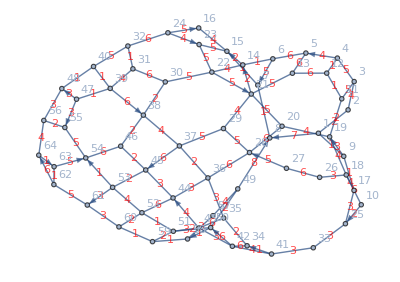

```mathematica
gr=Graph[{1<->2,1<->9,2<->3,9<->17,3<->4,17<->25,25<->33,5<->6,33<->41,7<->8,49<->57,10<->18,11<->12,18<->26,12<->13,34<->42,15<->16,17<->18,3<->11,18<->19,11<->19,19<->20,20<->21,35<->43,22<->23,43<->51,51<->59,4<->12,26<->27,20<->28,28<->29,28<->36,36<->44,30<->31,44<->52,31<->32,52<->60,5<->13,34<->35,13<->21,35<->36,21<->29,36<->37,29<->37,37<->38,45<->53,39<->40,41<->42,6<->14,42<->43,14<->22,22<->30,44<->45,30<->38,45<->46,38<->46,46<->54,49<->50,7<->15,50<->51,15<->23,51<->52,52<->53,31<->39,39<->47,54<->55,55<->56,57<->58,58<->59,59<->60,24<->32,60<->61,32<->40,61<->62,40<->48,62<->63,48<->56,56<->64,22->21,24->23,39->38,24->16,64->63,4->5,6->7,14->15,42->50,50->58,27->28,37->45,53->61,43->44,47->48,53->54,47->55,10->25,1->8,9->19,41->34,63->54,62->64,49->8,21->14},VertexLabels->"Name",EdgeWeight->{2,1,4,1,5,3,3,6,3,1,4,6,1,3,6,6,4,4,5,4,2,4,5,6,5,3,2,1,6,6,5,6,3,6,6,1,2,6,2,5,3,4,2,5,4,2,1,4,1,3,4,5,3,2,2,2,6,2,1,2,5,1,4,4,1,5,2,3,1,1,6,3,5,5,1,1,3,4,5,4,6,5,1,4,5,2,6,1,5,6,3,4,3,1,3,2,7,3,1,5,6,8,2},EdgeLabels->"EdgeWeight",EdgeLabelStyle->Red]
```

2 Найти пути от вершины v1 до вершины v2 (без учета весов ребер), используя алгоритмы 
   обхода в ширину и глубину . Указать время поиска (число пройденных вершин);
   	1) Обход в глубину

```mathematica
gr1=Graph[{1<->2,1<->9,2<->3,9<->17,3<->4,17<->25,25<->33,5<->6,33<->41,7<->8,49<->57,10<->18,11<->12,18<->26,12<->13,34<->42,15<->16,17<->18,3<->11,18<->19,11<->19,19<->20,20<->21,35<->43,22<->23,43<->51,51<->59,4<->12,26<->27,20<->28,28<->29,28<->36,36<->44,30<->31,44<->52,31<->32,52<->60,5<->13,34<->35,13<->21,35<->36,21<->29,36<->37,29<->37,37<->38,45<->53,39<->40,41<->42,6<->14,42<->43,14<->22,22<->30,44<->45,30<->38,45<->46,38<->46,46<->54,49<->50,7<->15,50<->51,15<->23,51<->52,52<->53,31<->39,39<->47,54<->55,55<->56,57<->58,58<->59,59<->60,24<->32,60<->61,32<->40,61<->62,40<->48,62<->63,48<->56,56<->64,22<->21,24<->23,39<->38,24<->16,64<->63,4<->5,6<->7,14<->15,42<->50,50<->58,27<->28,37<->45,53<->61,43<->44,47<->48,53<->54,47<->55,10<->25,1<->8,9<->19,41<->34,63<->54,62<->64,49<->8,21<->14},VertexLabels->"Name",EdgeWeight->{2,1,4,1,5,3,3,6,3,1,4,6,1,3,6,6,4,4,5,4,2,4,5,6,5,3,2,1,6,6,5,6,3,6,6,1,2,6,2,5,3,4,2,5,4,2,1,4,1,3,4,5,3,2,2,2,6,2,1,2,5,1,4,4,1,5,2,3,1,1,6,3,5,5,1,1,3,4,5,4,6,5,1,4,5,2,6,1,5,6,3,4,3,1,3,2,7,3,1,5,6,8,2},EdgeLabels->"EdgeWeight",EdgeLabelStyle->Red];
```

```mathematica
TreeGraph[First[Last[Reap[DepthFirstScan[gr1, 1, {"FrontierEdge" -> Sow}]]]], VertexLabels->"Name"]
```

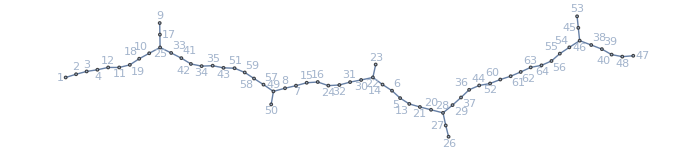

```mathematica
wayFirst={1,2,3,4,12,11,19,18,10,25,33,41,42,34,35,43,51,59,58,57,49,8,7,15,16,24,32,31,30,22,14,6,5,13,21,28,29,37,36,44,60,61,62,63};
Length[wayFirst]
```

44

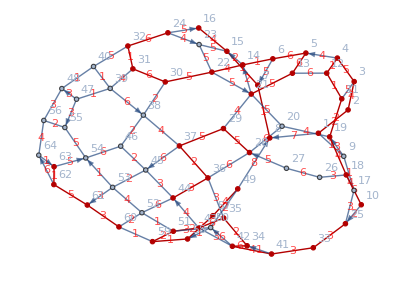

```mathematica
HighlightGraph[gr,Style[PathGraph[wayFirst]]]
```

```mathematica
TreeGraph[First[Last[Reap[BreadthFirstScan[gr1, 1, {"FrontierEdge" -> Sow}]]]], VertexLabels->"Name"]
```

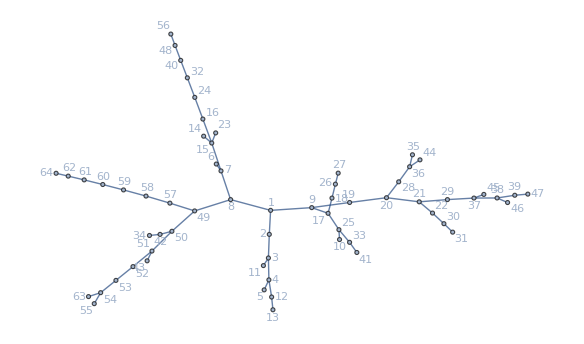

```mathematica
waySecond={1,8,49,50,42,52,53,54,63};
```

```mathematica
Length[waySecond]
```

9

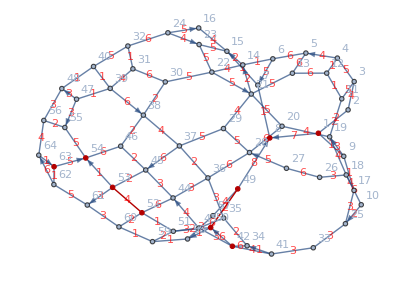

```mathematica
HighlightGraph[gr,Style[PathGraph[waySecond]]]
```

3 Найти кратчайший путь от вершины v1 до вершины v2 и его длину (с учетом весов ребер);

```mathematica
f=FindShortestPath[gr,1,63,Method->"Dijkstra"]
```

{1,9,17,25,33,41,42,43,51,52,60,61,62,63}

```mathematica
GraphDistance[gr,1,63]
```

33.

```mathematica
test={};
```

```mathematica
For[i=1,i<Length[f],i++,
AppendTo[test,GraphDistance[gr,f[[i]],f[[i+1]]]]]
Total[test]
```

33.

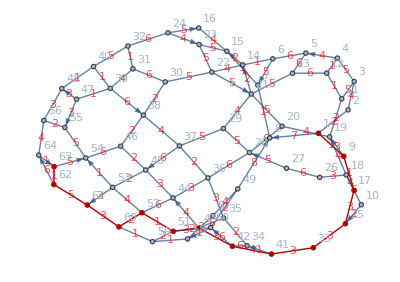

```mathematica
HighlightGraph[gr,Style[PathGraph[f]]]
```

4 Найти кратчайший замкнутый маршрут (маршрут коммивояжера) от вершины v1 через вершины v2, v3, v4 (в любой последовательности) и его длину;

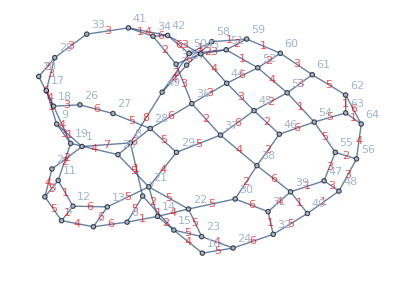

```mathematica
gr12=Graph[{1<->2,1<->9,2<->3,9<->17,3<->4,17<->25,25<->33,5<->6,33<->41,7<->8,49<->57,10<->18,11<->12,18<->26,12<->13,34<->42,15<->16,17<->18,3<->11,18<->19,11<->19,19<->20,20<->21,35<->43,22<->23,43<->51,51<->59,4<->12,26<->27,20<->28,28<->29,28<->36,36<->44,30<->31,44<->52,31<->32,52<->60,5<->13,34<->35,13<->21,35<->36,21<->29,36<->37,29<->37,37<->38,45<->53,39<->40,41<->42,6<->14,42<->43,14<->22,22<->30,44<->45,30<->38,45<->46,38<->46,46<->54,49<->50,7<->15,50<->51,15<->23,51<->52,52<->53,31<->39,39<->47,54<->55,55<->56,57<->58,58<->59,59<->60,24<->32,60<->61,32<->40,61<->62,40<->48,62<->63,48<->56,56<->64,22<->21,24<->23,39<->38,24<->16,64<->63,4<->5,6<->7,14<->15,42<->50,50<->58,27<->28,37<->45,53<->61,43<->44,47<->48,53<->54,47<->55,10<->25,1<->8,9<->19,41<->34,63<->54,62<->64,49<->8,21<->14},VertexLabels->"Name",EdgeWeight->{2,1,4,1,5,3,3,6,3,1,4,6,1,3,6,6,4,4,5,4,2,4,5,6,5,3,2,1,6,6,5,6,3,6,6,1,2,6,2,5,3,4,2,5,4,2,1,4,1,3,4,5,3,2,2,2,6,2,1,2,5,1,4,4,1,5,2,3,1,1,6,3,5,5,1,1,3,4,5,4,6,5,1,4,5,2,6,1,5,6,3,4,3,1,3,2,7,3,1,5,6,8,2},EdgeLabels->"EdgeWeight",EdgeLabelStyle->Red]
```

```mathematica
FindShortestTour[{1,21,63,50}]
```

{124,{1,4,3,2,1}}

```mathematica
gr1=FindShortestPath[gr,1,50,Method->"Dijkstra"]
```

{1,9,17,25,33,41,42,50}

```mathematica
gr2=FindShortestPath[gr,50,63,Method->"Dijkstra"]
```

{50,58,59,60,61,62,63}

```mathematica
gr3=FindShortestPath[gr,63,21,Method->"Dijkstra"]
```

{63,54,46,38,30,22,21}

```mathematica
gr4=FindShortestPath[gr,21,1,Method->"Dijkstra"]
```

{21,20,19,18,17,9,1}

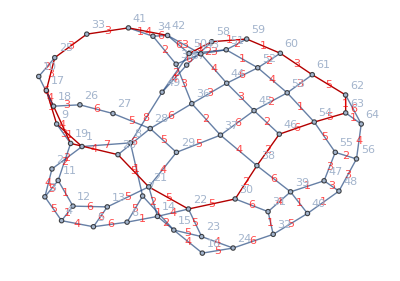

```mathematica
HighlightGraph[gr12,{1<->9,9<->17,17<->25,25<->33,33<->41,41<->42,50<->58,58<->59,59<->60,60<->61,61<->62,62<->63,63<->54,54<->46,46<->38,38<->30,30<->22,22<->21,21<->20,20<->19,19<->18,18<->17,17<->9,9<->1}]
```